# Existing Sea - Level models of Muon Flux distribution

REF:  Su, N., Liu, Y., Wang, L., Wu, B., & Cheng, J. (2021). A comparison of muon flux models at sea level for muon imaging and low background experiments. Front. Energy Res., 9, 750159.

## Parametrización de Flujo cósmico de muones y Dispersión Múltiple de Coulomb

#### Fórmula de Gaisser sin el Cos(θ), sin la correción esferica. Con E_µ>>ϵ_µ,ϵ_µ=1GeV y θ < 60°

con A_G=0.14, γ = 2.7, ϵ_π=115/1.1 GeV, ϵ_κ=810/1.1 GeV, B_G= 0.053

```mathematica
f[Emu_,θ_]:=0.14*(Emu)^-2.7*{1/(1+(1.1Emu*Cos[θ Degree])/115)+0.054/(1+(1.1Emu*Cos[θ Degree])/850)}
```

Gráfica de escala lineal, para θ = 0°

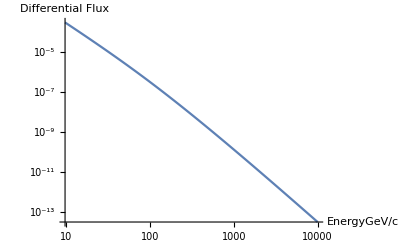

```mathematica
LogLogPlot[f[Emu,0],{Emu,0,10000},AxesLabel->{Text["EnergyGeV/c"],Text["Differential Flux"]}]
```

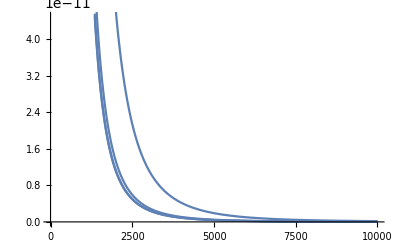

```mathematica
θ1=Plot[f[Emu,0],{Emu,0,10000}];
θ2=Plot[f[Emu,10],{Emu,0,10000}];
θ3=Plot[f[Emu,35],{Emu,0,10000}];
θ4=Plot[f[Emu,80],{Emu,0,10000}];
Show[θ1,θ2,θ3,θ4]
```

Gráfica con escala logarítmica en y ->  que es el flujo diferencial; x -> la energía.

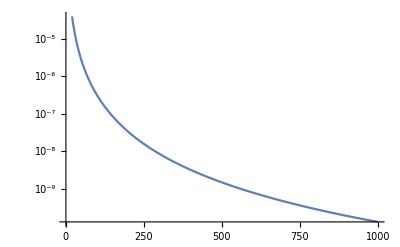

```mathematica
LogPlot[f[Emu,0],{Emu,1,1000}]
```

Gráfica con escala logarítmica en, x -> la energía ; y -> que es el flujo diferencial.

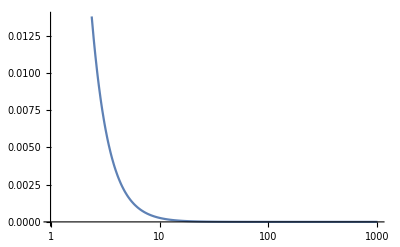

```mathematica
LogLinearPlot[f[Emu,0],{Emu,1,1000}]
```

Gráfica con escala logarítmica en x - y .

```mathematica
Log
```

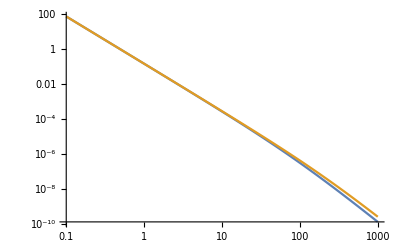

```mathematica
LogLogPlot[{f[Emu,0],f[Emu,65]},{Emu,0.1,1000}]
```

Fórmula de Gaisser-Tang con el Cos (θ), de la correción esferica .

```mathematica
p1=0.102573; p2=-0.068287;p3=0.958633;p4=0.0407253;p5=0.817285;
```

```mathematica
Cosθ[θ_]:=Sqrt[(Cos[θ ]^2+p1^2+p2 Cos[θ ]^p3+p4 Cos[θ ]^p5)/(1+p1^2+p2+p4)];
```

```mathematica
Emu2[Emu_,θ_]:= Emu*(1+(3.64 (*GeV*))/(Emu  Cosθ[θ *π/180]^1.29));
```

```mathematica
FlujoMu[Emu_,θ_]:=0.14 (Emu2[Emu,θ]/(1(*GeV*)))^-2.7*(1/(1+(1.1* Emu *Cosθ[θ *π/180])/(115 (*GeV*)))+0.054/(1+(1.1* Emu *Cosθ[θ *π/180])/(850(*GeV*))))
```

Para 0 ° y 75 ° grados . De 1 GeV a 600 GeV

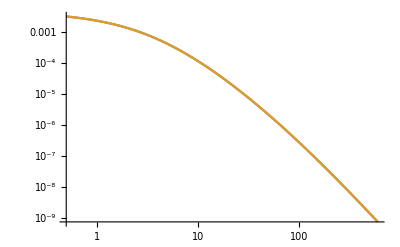

```mathematica
LogLogPlot[{FlujoMu[Emu,0],FlujoMu[Emu,75]},{Emu,0.5,600},GridLines->Automatic,PlotRange->All]
```

#### Usando dispersión múltiple de Coulomb para segregar materiales de Alto, Medio y Bajo número atómico Z

Al salir del material, la nueva trayectoria del muón puede describirse mediante los ángulos de dispersión proyectados θx, θy y los desplazamientos ∆x, ∆y donde todos estos [REF: Schultz, Thesis, Cosmic Ray Radiography].

Una aproximación gaussiana simple funciona bien para el 98 % central de la distribución de dispersión. Para uno de los ángulos de dispersión proyectados, θx :

f_θ_x(θ_x)≅1/(√(2π)σ_θ)exp(-θ_x^2/(2 σ_θ^2))

De misma forma el ángulo proyectado  θy, es independiente pero idénticamentedistribuido a θx.

f_θ_y(θ_y)≅1/(√(2π)σ_θ)exp(-θ_y^2/(2 σ_θ^2))

De forma que para los dos planos es:

f_θ(θ)≅1/(√(2π)σ_θ)exp(-θ^2/(2 σ_θ^2))

Que es definida para una media(μ = 0) y varianza σ_θ^2. Según,  [REF: Bae,Momentum-Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer].

f(θ| 0,σ_θ^2)=1/(√(2π)σ_θ)exp(-1/2 *θ^2/σ_θ^2)   ;
 σ_θ = (13.6 MeV)/(β_μ p_μ c)√(L/L_o)[1+0.088Log(L/L_o)]

θ -> ángulo de dispersión, σ_θ-> es el ancho de la Distro. de Gauss de dispersión, 
L -> grosor del medio de dispersión, Lo-> longitud de radiación, β_μ-> el la taza del velocidad de la luz del muon(c), p_μ->momento del muon.

Según, [REF : Bonomi, Apps . cosmic - ray muons, Review ...] y [REF : Particle Data Group], el RMS(σ) es. La raíz cuadrada media (rms) de la aproximación gaussiana de la distribución angular proyectada se ha calculado y se puede expresar de la siguiente manera .

σ_θ=(13.6MeV)/βcp*z*√(X/Xo)*(1+0.038*ln((x z^2)/(Xo β^2)))
X -> grosor del medio de dispersión, Xo-> longitud de radiación, βc->  velocidad del muon(~1),z->carga de la psrtícula (muon es 1), p->momento del muon.

#### Gráfica de Gauss de ángulo de dispersión, Para un medio de 10 cm de Pb [REF : Bae, Momentum - Dependent ...]

Ecuacion según [ REF : Bae, Momentum - Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer]

```mathematica
(*Constantes*)βc= 1(*factor beta de luz*);L=10(*grosor cm*);Lo=6.37 (*Lrad, Pb g/cm^2*);p=3*10^9(*momento 3GeV, TODO en eV*);StdSigma=(13.6*10^6)/(βc*p)*√(L/Lo)*(1+0.088*Log[L/Lo]);
f[θ_]:=1/(√(2*π)*StdSigma)*Exp[-1/2*θ^2/StdSigma^2];
```

¡ OJO ! el término de la exponencial se hace muy chiquito  ya que la expresión de la varianza es muy grande y contribuye de maner sustancial a la forma aprox. de  ⅇ^(-α θ^2), para un α muy grande, lo cual genera valores muy pequeños.

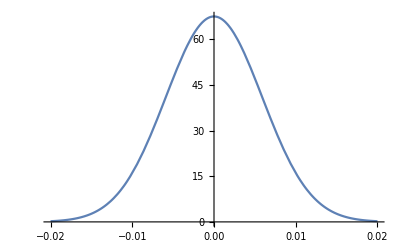

```mathematica
Plot[f[θ],{θ,-2*10^-2,2*10^-2}]
```

Entonces deben de existir ángulos en el orden de 10^-2a 10^-3rads. Para que no explote la Gauss.

#### Gráfica de Gauss de ángulo de dispersión, Para un medio de 10 cm de Pb [REF : Bonomi, Apps. cosmic-ray muons, Review ...] y [REF : PDG, Review of Particle Physics, cosmic-ray muons ...]

Ejemplo.

```mathematica
(*Constantes*)βc= 1(*factor beta de luz*);β=1;X=10(*grosor cm*);Xo=6.37 (*Lrad, Pb g/cm^2*);p=3*10^9(*momento 3GeV*);z=1(*carga*);StdSigma2=(13.6*10^6)/(βc*p)*z*√(X/Xo)*(1+0.038*Log[ⅇ,(X*z^2)/(Xo*β^2)]);ff[θ_]:=1/(√(2*π)*StdSigma2)*Exp[-θ^2/(2*StdSigma2^2)];
```

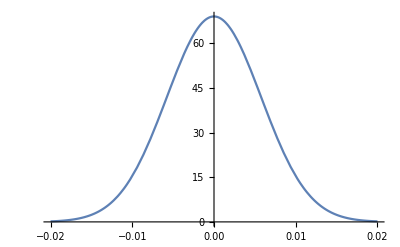

```mathematica
Plot[ff[θ],{θ,-2*10^-2,2*10^-2}]
```

#### OTRO Para 10 cm de Pb

```mathematica
DataTheta=RandomVariate[NormalDistribution[0,StdSigma2],3*10^3];
```

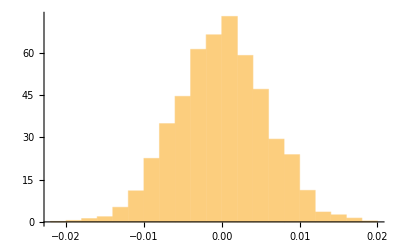

```mathematica
Histogram[DataTheta,20,"ProbabilityDensity"]
```

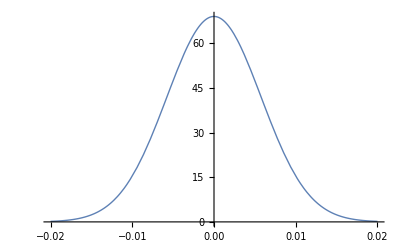

```mathematica
Plot[PDF[NormalDistribution[0,StdSigma2],x],{x,-2*10^-2,2*10^-2},PlotStyle->Thick]
```

#### 10 cm Pb, y 10 cm Si, momento de 3GeV

```mathematica
StdSigmaPb=(13.6*10^6)/(βc*p)*√(10/Xo)*(1+0.038*Log[ⅇ,(10*z^2)/(Xo*β^2)]);(*Pb*)
StdSigmaSi=(13.6*10^6)/(βc*p)*√(10/21.82)*(1+0.038*Log[ⅇ,(10*z^2)/(21.82*β^2)]);(*Si*)
```

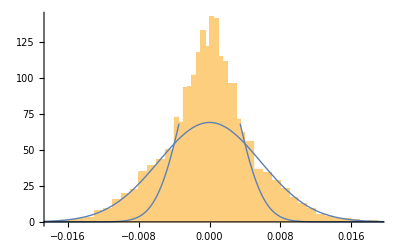

```mathematica
DataPb=RandomVariate[NormalDistribution[0,StdSigmaPb],3*10^3];
DataSi=RandomVariate[NormalDistribution[0,StdSigmaSi],3*10^3];
HistPb=Histogram[DataPb,30,"ProbabilityDensity"];
HistSi=Histogram[DataSi,30,"ProbabilityDensity"];
PDFPb=Plot[PDF[NormalDistribution[0,StdSigmaPb],x],{x,-2*10^-2,2*10^-2},PlotStyle->Thick];
PDFSi=Plot[PDF[NormalDistribution[0,StdSigmaSi],x],{x,-3*10^-2,3*10^-2},PlotStyle->Thick];
Show[{HistPb,HistSi,PDFPb,PDFSi}]
```

#### Cálculo de la varianza y gráfica FALLIDO

Cálculo de la varianza de dispersión en función del grosor del material de dispersión, de plomo.

```mathematica
(*Constantes*)β = 1;cLight = 1;(*Longt. rads de Pb->tablas [g/cm^2]]*)L0=6.37 ;
```

```mathematica
VarSigma[Thickness_,pMomentum_]:=(0.0136/(β*pMomentum*cLight)√(Thickness/L0)(1+0.088*Log[10,Thickness/L0]))^2;
```

```mathematica
DesvSigma[Thickness_,pMomentum_]:=0.0136/(β*pMomentum*cLight)√(Thickness/L0)(1+0.088*Log[10,Thickness/L0]);
```

```mathematica
{DesvSigma[0.1,3],VarSigma[0.1,3]*10^3}
```

{0.000360357,0.000129857}

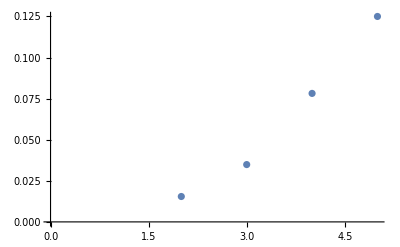

```mathematica
ListPlot[Table[VarSigma[L,3]*10^3,{L,{0,5,10,20,30}}]]
```

Con las funciones de arriba no es posible reproducir la gráfica de la varianza del ángulo de dispersión de [REF : Bae, Momentum - Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer].

Al parecer hay que seguir una construcción de varianza descrito en [REF : Bae, The Effect of Cosmic Ray Muon Momentum Measurement for Monitoring Shielded Special
   Nuclear Materials].